```mathematica
ResourceFunction["MaTeXInstall"][]
```

10

1+p+p^2+p^3+p^4+p^5+p^6+p^7+p^8

324 (1-p) p^17

324 (1-p) p^17

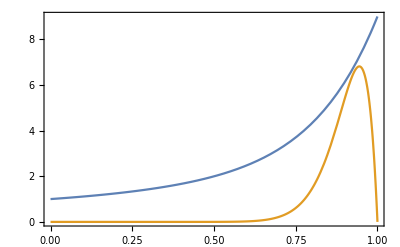

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all10.eps

```mathematica
<<MaTeX`
n = 10
DALL[p_,m_] = Sum[p^(i-1),{i,1,m}] 
LowerBound[p_,m_]=4*p(1-p)(m*p^(m-1))^2
LowerBound[p,n]
plot1 = Plot[{DALL[p,n], LowerBound[p,n]},{p,0,1},PlotLegends->{MaTeX@{"D_p(ALL_{10}^1)","4p(1-p)(\mathbf{I}^p(ALL_{10}^1))^2"}},Frame -> True,FrameLabel->{MaTeX@"p", MaTeX@"D_p(f)"},LabelStyle->{Black,Medium} ]
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all10.eps",plot1]
```